I want to understand how to solve a partially reduced Sylvester equation from

Golub, G.; Nash, S.; Loan, C. Van (1979). “A Hessenberg–Schur method for the problem AX + XB= C”. IEEE Transactions on Automatic Control. 24 (6): 909–913. doi:10.1109/TAC.1979.1102170. hdl:1813/7472. ISSN 0018-9286.

@ARTICLE{1102170,
  author={Golub, G. and Nash, S. and Van Loan, C.},
  journal={IEEE Transactions on Automatic Control}, 
  title={A Hessenberg-Schur method for the problem AX + XB= C}, 
  year={1979},
  volume={24},
  number={6},
  pages={909-913},
  doi={10.1109/TAC.1979.1102170}}

The reduction is easy.  An efficient solve of the Hessenberg Sylvester is less obvious.

## Hessenberg Reduction

1.04634×10^-14

9.96389×10^-15

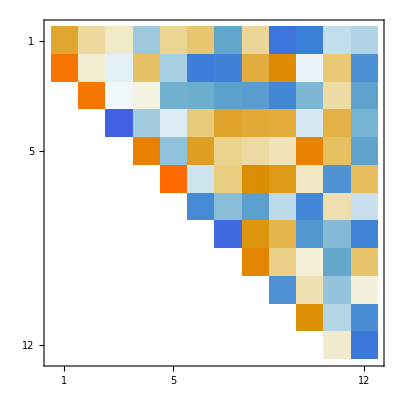
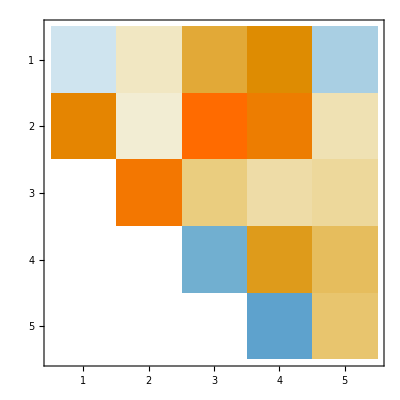

```mathematica
{m,n}={12,5};
{A,B,X}=Map[RandomReal[{-1,1},#]&,{{m,m},{n,n},{m,n}}];
RHS=A.X+X.B;
Norm[X-LyapunovSolve[A,B,RHS]]
{{QA,HA},{QB,HB}}=Map[HessenbergDecomposition,{A,B}];
Map[Norm,{A-QA.HA.QAᵀ,B-QB.HB.QBᵀ}];
(* Solved Reduced Equation *)
Norm[X-QA.LyapunovSolve[HA,HB,QAᵀ.RHS.QB].QBᵀ]
Map[MatrixPlot,{HA,HB}]
```

## Triangular Back Solve: Not Sylvester

If T x=b with T triangular then the last (bottom) equation is 
	T_(m,m)x_m=b_m⟺x_m=b_m/(T_(m,m))
and the second last is 
	T_(m-1,m-1)x_(m-1)+T_(m-1,m)x_(m-1)=b_(m-1)⟺x_(m-1)=1/(T_(m-1,m-1))(b_(m-1)-T_(m-1,m)x_m)
which can be evaluated sequentially.

```mathematica
BackSubT[T_,b_]:=Module[{x=0.0*b,m=Length[b]},
Do[
x⟦i⟧=1/T⟦i,i⟧(b⟦i⟧-Sum[T⟦i,j⟧ x⟦j⟧,{j,i+1,m}]),
{i,m,1,-1}];
x
]
```

Testing

```mathematica
m=126;
x=RandomReal[{-1,1},m];
T=UpperTriangularize[RandomReal[{-1,1},{m,m}]]+20IdentityMatrix[m];
b=T.x;
xMma=LinearSolve[T,b];
xT = BackSubT[T,b];
Map[Norm,{x-xMma,x-xT,xMma-xT}]
```

{3.1105×10^-15,1.39906×10^-15,3.23296×10^-15}

## Hessenberg Back Solve

A Hessenberg BackSolve (I know I saw this somewhere).  Assign a symbolic value to the last entry and solve with that symbolic value in place.

If H x=b with H upper Hessenberg then the last (bottom) equation is 
	H_(m,m)x_m+H_(m,m-1)x_(m-1)=b_m⟺x_(m-1)=b_m/(H_(m,m-1))-(H_(m,m))/(H_(m,m-1))x_m
and the second last is 
	H_(m-1,m)x_m+H_(m-1,m-1)x_(m-1)+H_(m-1,m-2)x_(m-2)=b_(m-1)⟺x_(m-2)=(b_(m-1))/(H_(m-1,m-2))-(H_(m-1,m))/(H_(m,m-2))x_m-(H_(m-1,m-1))/(H_(m,m-2))x_(m-1)
which can be evaluated sequentially.

Here is a preliminary manual “script”.

```mathematica
m=11;
H=UpperTriangularize[RandomReal[{-1,1},{m,m}],-1];
x=RandomReal[{-1,1},m];
b=H.x;
xNew=0*x;
Clear[γ]
xNew⟦m⟧=γ;
xNew⟦m-1⟧=Expand[1/H⟦m,m-1⟧(b⟦m⟧-H⟦m,m⟧xNew⟦m⟧)];
xNew⟦m-2⟧=Expand[1/H⟦m-1,m-2⟧(b⟦m-1⟧-H⟦m-1,m⟧xNew⟦m⟧-H⟦m-1,m-1⟧xNew⟦m-1⟧)];
xNew⟦m-3⟧=Expand[1/H⟦m-2,m-3⟧(b⟦m-2⟧-H⟦m-2,m⟧xNew⟦m⟧-H⟦m-2,m-1⟧xNew⟦m-1⟧-H⟦m-2,m-2⟧xNew⟦m-2⟧)];
xNew⟦m-4⟧=Expand[1/H⟦m-3,m-4⟧(b⟦m-3⟧-H⟦m-3,m⟧xNew⟦m⟧-H⟦m-3,m-1⟧xNew⟦m-1⟧-H⟦m-3,m-2⟧xNew⟦m-2⟧-H⟦m-3,m-3⟧xNew⟦m-3⟧)];
xNew⟦-5;;-1⟧/.γ->x⟦-1⟧
x⟦-5;;-1⟧
```

{-0.344509,-0.826057,0.0993876,-0.367893,-0.597411}

{-0.344509,-0.826057,0.0993876,-0.367893,-0.597411}

Here is the “symbolic” version with a loop.

```mathematica
m=8;
H=UpperTriangularize[RandomReal[{-1,1},{m,m}],-1];
x=RandomReal[{-1,1},m];
b=H.x;
xNew=0*x;
Clear[γ]
xNew⟦m⟧=γ;
Do[
xNew⟦m-i⟧=Expand[1/H⟦m+1-i,m-i⟧(b⟦m+1-i⟧-H⟦m+1-i,All⟧.xNew)],
{i,1,m-1}]
Norm[x-xNew/.γ->x⟦-1⟧]
```

1.34675×10^-15

Here is a loop (again “analytic”) that does not bounce any zeros.

```mathematica
m=8;
H=UpperTriangularize[RandomReal[{-1,1},{m,m}],-1];
x=RandomReal[{-1,1},m];
b=H.x;
xNew=0*x;
Clear[γ]
xNew⟦m⟧=γ;
Do[
xNew⟦m-i⟧=Expand[1/H⟦m+1-i,m-i⟧(b⟦m+1-i⟧-H⟦m+1-i,m-i+1;;m⟧.xNew⟦m-i+1;;m⟧)],
{i,1,m-1}]
Norm[x-xNew/.γ->x⟦-1⟧]
```

I need to “vector” the analytic bit.

```mathematica
m=8;
H=UpperTriangularize[RandomReal[{-1,1},{m,m}],-1];
x=RandomReal[{-1,1},m];
b=H.x;
xVec=ConstantArray[{0,0},m];
xNew=ConstantArray[0,m];
Clear[γ]
xNew⟦m⟧=γ;
Do[
xNew⟦m-i⟧=Expand[1/H⟦m+1-i,m-i⟧(b⟦m+1-i⟧-H⟦m+1-i,m-i+1;;m⟧.xNew⟦m-i+1;;m⟧)],
{i,1,m-1}]
Expand[H.xNew]
b
Norm[x-xNew/.γ->x⟦-1⟧]
```

{5.93756-12.8833 γ,-1.64361,-0.246642,-0.626371+4.44089×10^-16 γ,-0.262598,-0.669888,0.1269,0.576361}

{1.82138,-1.64361,-0.246642,-0.626371,-0.262598,-0.669888,0.1269,0.576361}

1.78263×10^-15

```mathematica
m=11;
H=UpperTriangularize[RandomReal[{-1,1},{m,m}],-1];
x=RandomReal[{-1,1},m];
b=H.x;
xNew=0*x;
Clear[γ]
xNew⟦m⟧=γ;
Do[
xNew⟦m-i⟧=Expand[1/H⟦m+1-i,m-i⟧(b⟦m-i⟧-H⟦m+1-i,All⟧.xNew)],
{i,1,5}]
xNew⟦m-5;;m⟧/.γ->x⟦-1⟧
x⟦m-5;;m⟧
```

{-1.06571,2.94965,-6.05147,-0.366664,0.132798,0.0439565}

{0.395471,0.43036,-0.799502,-0.120817,-0.190989,0.0439565}

Here is a preliminary “script”.

```mathematica
Clear[xNew,m,γ]
m=4;
H=HessenbergDecomposition[RandomReal[{-1,1},{m,m}]]⟦2⟧;
x=RandomReal[{-1,1},m];b=H.x;
xNew=ConstantArray[0,m];
xNew⟦m⟧=γ;
Do[
xNew⟦m-i⟧=Expand[(b⟦m+1-i⟧-H⟦m-i,All⟧.xNew)/H⟦m-i+1,m-i⟧],
{i,1,m-1}];
{x,xNew/.γ->x⟦-1⟧}
```

{{-0.699193,-0.585399,0.672587,0.254964},{38.1885,35.1596,41.5099,0.254964}}

```mathematica
xNew⟦m-1⟧=Expand[1/H⟦m,m-1⟧(b⟦m⟧-H⟦m,m⟧xNew⟦m⟧)];
xNew⟦m-2⟧=Expand[1/H⟦m-1,m-2⟧(b⟦m-1⟧-H⟦m-1,m⟧xNew⟦m⟧-H⟦m-1,m-1⟧xNew⟦m-1⟧)];
xNew⟦m-3⟧=Expand[1/H⟦m-2,m-3⟧(b⟦m-2⟧-H⟦m-2,m⟧xNew⟦m⟧-H⟦m-2,m-1⟧xNew⟦m-1⟧-H⟦m-2,m-2⟧xNew⟦m-2⟧)];
xNew⟦m-4⟧=Expand[1/H⟦m-3,m-4⟧(b⟦m-3⟧-H⟦m-3,m⟧xNew⟦m⟧-H⟦m-3,m-1⟧xNew⟦m-1⟧-H⟦m-3,m-2⟧xNew⟦m-2⟧-H⟦m-3,m-3⟧xNew⟦m-3⟧)];
xNew⟦-5;;-1⟧/.γ->x⟦-1⟧
x⟦-5;;-1⟧
```

```mathematica
BackSubH[H_,b_]:=Module[{x=0.0*{b,b}ᵀ,m=Length[b]},
x⟦m⟧={0,1};
Do[
x⟦i-1⟧=1/H⟦i,i-1⟧({b⟦i⟧,0}-Sum[{H⟦i,j⟧,0} x⟦j⟧,{j,i,m}]),
{i,m,2,-1}];
x
]
```

```mathematica
m=11;
H=UpperTriangularize[RandomReal[{-1,1},{m,m}],-1];
x=RandomReal[{-1,1},m];
b=H.x;
Clear[γ]
xMma=LinearSolve[H,b]
{c0,cγ}=BackSubH[H,b]ᵀ;
c0+x⟦-1⟧ cγ
```

{0.561683,-0.821452,-0.557227,0.936466,-0.327703,-0.516467,-0.568562,-0.7105,0.31593,0.82063,0.852904}

{35.6026,24.3897,13.5744,-23.8645,9.83088,-0.00836211,0.987216,4.04016,3.52559,4.89516,0.852904}

## Triangular Sylvester Solve

If S X+X L=B with L Lower Triangular and x∈ℝ^(m×n) then the n^th column of 
	S (x_1 | x_2 | … | x_n)+X L=(b_1 | b_2 | … | b_n)
is simply
	S x_n+L_(n,n)x_n=b_n
so we can compute the last column by solving 
	(S+L_nn I)x_n=b_n
This can be assembled recursively just like a triangular back solve.  The second last column of the equation is
	S x_(n-1)+L_(n-1,n-1)x_(n-1)+ L_(n-1,n)x_n=b_(n-1)

Notes: Somehow I only need to have one of the matrices structured to get this started. This seems like a very inexpensive lunch.

```mathematica
{m,n}={3,4};
X=Array[x,{m,n}];
S=Array[s,{m,m}];
L=LowerTriangularize[Array[l,{n,n}]];
Map[Norm,{(S.X)⟦All,n⟧ -S.X⟦All,n⟧,(X.L)⟦All,n⟧-L⟦n,n⟧ X⟦All,n⟧}]
```

{0,0}

```mathematica
{m,n}={3,4};
X=Array[x,{m,n}];
S=Array[s,{m,m}];
L=LowerTriangularize[Array[l,{n,n}]];
Map[Norm,{(S.X)⟦All,n-1⟧ -S.X⟦All,n-1⟧}]
```

{0}

```mathematica
(X.L)⟦All,n-1⟧-L⟦n-1,n-1⟧ X⟦All,n-1⟧-L⟦n,n-1⟧ X⟦All,n⟧
```

{0,0,0}

```mathematica
{m,n}={3,4};
X=RandomReal[{-1,1},{m,n}];
S=RandomReal[{-1,1},{m,m}];
T=UpperTriangularize[RandomReal[{-1,1},{n,n}]];
B=S.X+X.T;
```

{{0.327212,-0.424941,0.453203,0.964165},{-0.583473,-1.06562,-0.543987,-0.791055},{0.418656,0.139383,0.304786,0.0601531}}

```mathematica
BackSubT[T_,b_]:=Module[{x=0.0*b,m=Length[b]},
Do[
x⟦i⟧=1/T⟦i,i⟧(b⟦i⟧-Sum[T⟦i,j⟧ x⟦j⟧,{j,i+1,m}]),
{i,m,1,-1}];
x
]
```

Testing

```mathematica
m=126;
x=RandomReal[{-1,1},m];
T=UpperTriangularize[RandomReal[{-1,1},{m,m}]]+20IdentityMatrix[m];
b=T.x;
xMma=LinearSolve[T,b];
xT = BackSubT[T,b];
Map[Norm,{x-xMma,x-xT,xMma-xT}]
```

{3.1105×10^-15,1.39906×10^-15,3.23296×10^-15}